# Problem Set 02

## Forwards and backwards time

Sketch solutions showing both  t → ∞ and t → -∞.  I start by plotting some approximate numerical solutions in forward time.  I’ll start plotting from t = 0.5 (there is nothing special about this choice of starting time).

### Forward time

ParametricNDSolve::ndsz: At t == 1.69895, step size is effectively zero; singularity or stiff system suspected.

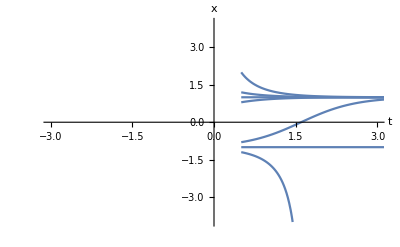

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
delt = 0.2;
plots = {};
f[x_] = 1-x^2;
x0 = {-1-delt, -1, -1+delt, 1-delt, 1,1+delt,2};
  (* set up a six different initial conditions *)
solforward = ParametricNDSolve[{x'[t]==f[x[t]],x[0.5]==xinit},x,{t,0.5,4},xinit,Method->"BDF"];
Do[solx=x[x0[[val]]]/.solforward;
{begintime,endtime} = solx["Domain"][[1]]; 
(* some trajectories diverge, so find the range of time over which the integration worked *)
AppendTo[plots,Plot[solx[t],{t,begintime,endtime},PlotRange->{{0,3},{-4,4}}]],{val,1,Length[x0]}];
(* use that time range over which integration worked to do the plotting *) 
Show[plots,AxesLabel->{t, x},LabelStyle->Medium,PlotRange->{{-3,3},{-4,4}}]
```

### Backwards time

The backwards time system.  t = 0.5 is equivalent to t1 = -0.5, so start this system at time -0.5.  The differential equation has the time reversal.

ParametricNDSolve::ndsz: At t1 == 0.698947, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolve::ndsz: At t1 == 0.0493059, step size is effectively zero; singularity or stiff system suspected.

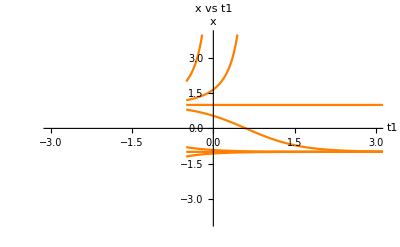

```mathematica
delt = 0.2;
plotnew = {};
solbackward = ParametricNDSolve[{x'[t1]==-f[x[t1]],x[-0.5]==xinit},x,{t1,-0.5,4},xinit,Method->"BDF"];
Do[solx=x[x0[[val]]]/.solbackward;
{begintime,endtime} = solx["Domain"][[1]]; 
AppendTo[plotnew,Plot[solx[t1],{t1,begintime,endtime},PlotRange->{{0,3},{-4,4}},PlotStyle->Orange]];
AppendTo[plots,Plot[solx[-t],{t,-endtime,-begintime},PlotRange->{{0,3},{-4,4}},PlotStyle->Orange]]
(*t1 ∈ [begintime,endtime] is equivalent to t ∈ [-endtime,-begintime].  For example, t1 ∈ [-2,4] is equivalent to t ∈ [-4,2] *),{val,1,Length[x0]}];
Show[plotnew,AxesLabel->{t1, x},PlotRange->{{-3,3},{-4,4}},PlotLabel->"x vs t1"]
```

### Plot solutions x vs t

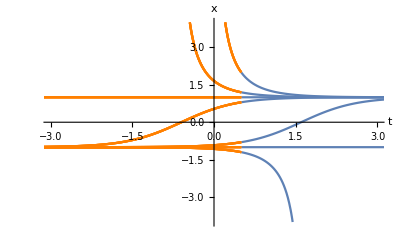

```mathematica
Show[plots,AxesLabel->{t, x},LabelStyle->Medium,PlotRange->{{-3,3},{-4,4}}]
```

The forward time behavior of the solutions is in blue and the backwards time behavior is in orange.  In backwards time, solutions move away from x = 1 and approach x = -1.  In forwards time solutions approach x = 1 and leave x = -1.
Notice that all solution curves are continuous through the starting time (which was t = 0.5 for these simulations).

## Question 3: stability diagram.

We are adding a parameter to a pitchfork.

### shape of the bifurcation diagrams (but not the actual diagrams)

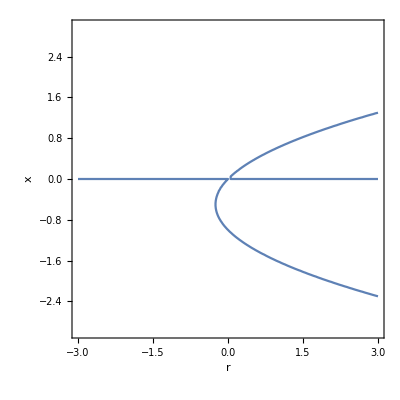

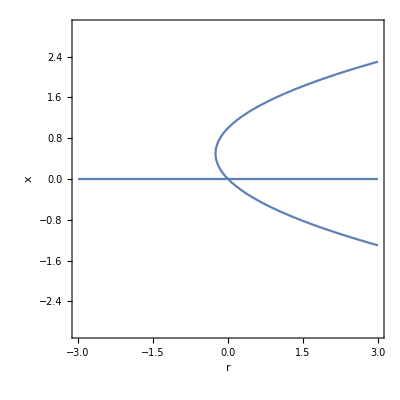

```mathematica
p1=ContourPlot[r x - 1 x^2 - x^3==0,{r,-3,3},{x,-3,3},PlotPoints->30,FrameLabel->{r,x}]
p2=ContourPlot[r x + 1 x^2 - x^3==0,{r,-3,3},{x,-3,3},PlotPoints->30,FrameLabel->{r,x}]
```

x = 0 is always a fixed point.  It undergoes a transcritical bifurcation at r = 0.
Then there is a parabola of fixed points (with a saddle node bifurcation at the r value associated with the vertex).
The vertex of the parabola: r - a x - x^2 = 0, r = a x + x^2.  Minimum when a + 2x = 0 so x = -a/2 so r = a(-a/2)+(-a/2)^2 = -a^2/2+a^2/4 = -a^2/4.  Let’s check that by plotting that point on the bifurcation diagram...

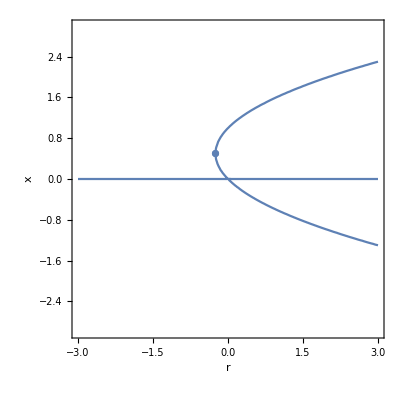

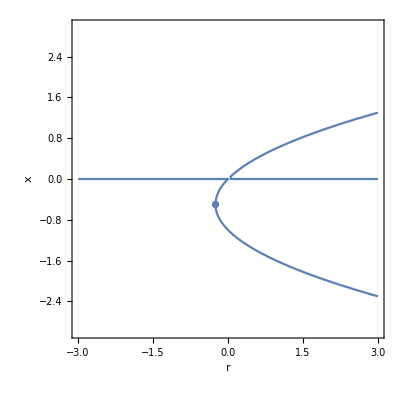

```mathematica
Show[p2,ListPlot[{{-a^2/4,-a/2}/.a->-1}]]
Show[p1,ListPlot[{{-a^2/4,-a/2}/.a->1}]]
```

I did successfully locate the bifurcation...
The bifurcation happens when r = -a^2/4.  I can plot the curve of locations in (r a)-space where it happens...

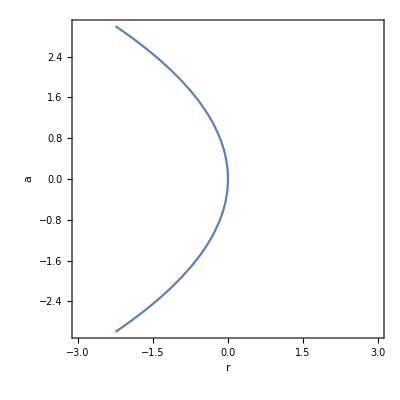

```mathematica
p3=ContourPlot[r==-a^2/4,{r,-3,3},{a,-3,3},FrameLabel->{r, a}]
```

Let me add the cases I did above (a = 1, r = -1/4 and a = -1, r = -1/4).

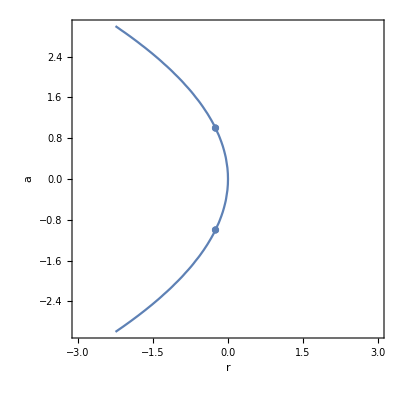

```mathematica
Show[p3,ListPlot[{{-a^2/4,a}/.a->1}],ListPlot[{{-a^2/4,a}/.a->-1}]]
```

The stability diagram also should have the transcritical bifurcation when r = 0, so the plot above is not the complete diagram.

## Question 4: bifurcation diagrams and stability diagram.

I will provide the shape of the bifurcation diagrams, but not the actual bifurcation diagrams (which would include stability information).

### r = 0.6

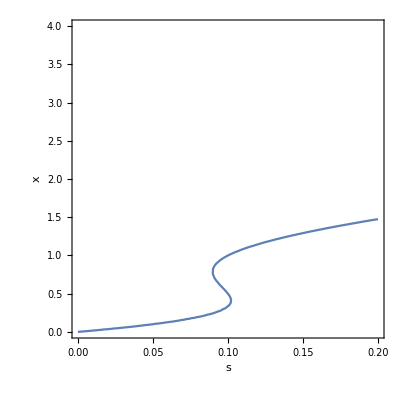

```mathematica
rval = 0.6;
p0 = ContourPlot[s - rval x +x^2/(1+x^2)==0,{s,0,0.2},{x,0,4},PlotPoints->30,FrameLabel->{s,x}]
```

I chose an r value of 0.6.  You can see two saddle node bifurcations in the diagram.  Let me add approximate locations for those points so that they are more visible.

```mathematica
bifnpoints = NSolve[{s - rval x +x^2/(1+x^2)==0,D[s - rval x +x^2/(1+x^2),x]==0},{s,x}]
```

{{x→-0.598-1.65866 ⅈ,s→-1.59591-1.33273 ⅈ},{x→-0.598+1.65866 ⅈ,s→-1.59591+1.33273 ⅈ},{x→0.787553,s→0.0897244},{x→0.408447,s→0.102092}}

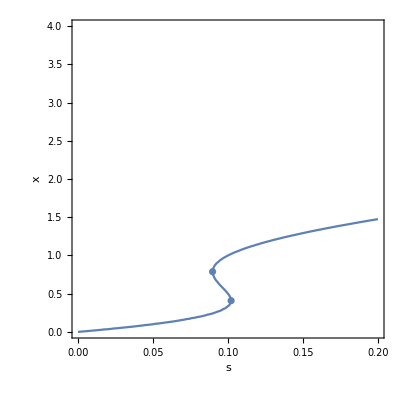

```mathematica
Show[p0,ListPlot[{s,x}/.bifnpoints]]
```

In the diagram above, I have the locations of fixed points in sx-space (but no stability information), and I have marked the locations of the saddle-node bifurcations with dots.

I can also put the locations of the bifurcations on a stability diagram: they occur when r = 0.6

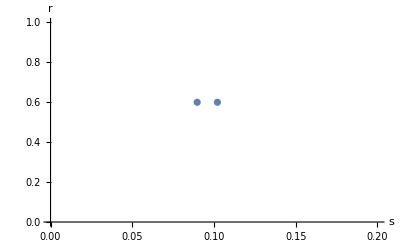

```mathematica
stab1 = ListPlot[{s,0.6}/.bifnpoints,PlotRange->{{0,0.2},{0,1}},AxesLabel->{s,r}]
```

### r = 0.4

{{x→-0.713314-1.80588 ⅈ,s→-1.46583-0.987726 ⅈ},{x→-0.713314+1.80588 ⅈ,s→-1.46583+0.987726 ⅈ},{x→1.20684,s→-0.110175},{x→0.21979,s→0.0418344}}

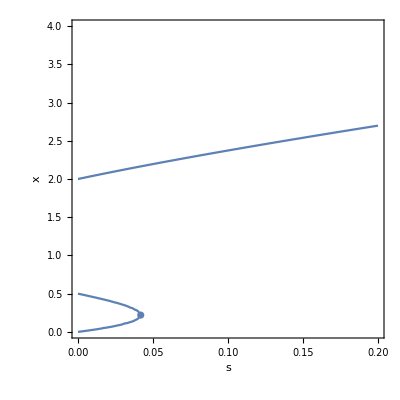

```mathematica
rval = 0.4;
p1 = ContourPlot[s - rval x +x^2/(1+x^2)==0,{s,0,0.2},{x,0,4},PlotPoints->30,FrameLabel->{s,x}];
bifnpoints1 = NSolve[{s - rval x +x^2/(1+x^2)==0,D[s - rval x +x^2/(1+x^2),x]==0},{s,x}]
Show[p1,ListPlot[{s,x}/.bifnpoints1
]]
```

In the diagram above, I have the locations of fixed points in sx-space (but no stability information), and I have marked the locations of the saddle-node bifurcations with a dot.

I can also put the location of the bifurcation on the stability diagram: it occurs when r = 0.4

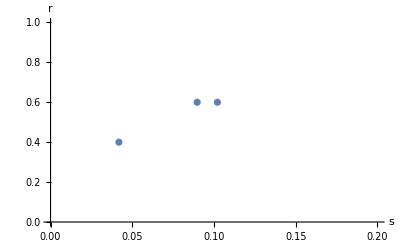

```mathematica
stab2 = ListPlot[{s,rval}/.bifnpoints1,PlotRange->{{0,0.2},{0,1}}];
Show[stab1,stab2]
```

### stability diagram

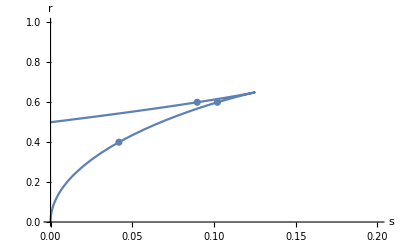

```mathematica
Show[stab1,stab2,ParametricPlot[{x^2(1-x^2)/(1+x^2)^2,2x/(1+x^2)^2},{x,0,1}]]
```

Notice that the bifurcation locations we found above sit on the curves in the stability diagram.  The diagram shows where the bifurcations occur in sr-space.  

For example, we can see from the stability diagram that at r = 0.2 there will be one bifurcation for s>0 and it occurs at about s = 0.01 or so.

{{x→-0.951593-2.12901 ⅈ,s→-1.30298-0.599555 ⅈ},{x→-0.951593+2.12901 ⅈ,s→-1.30298+0.599555 ⅈ},{x→1.80109,s→-0.404151},{x→0.102096,s→0.0101031}}

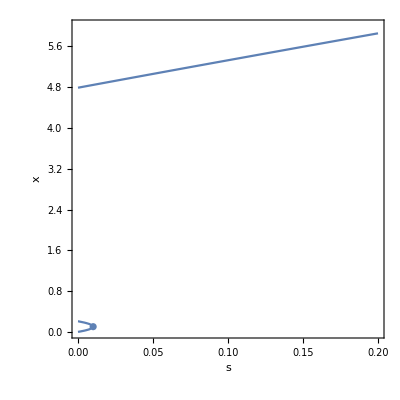

```mathematica
rval = 0.2;
p1 = ContourPlot[s - rval x +x^2/(1+x^2)==0,{s,0,0.2},{x,0,6},PlotPoints->30,FrameLabel->{s,x}];
bifnpoints1 = NSolve[{s - rval x +x^2/(1+x^2)==0,D[s - rval x +x^2/(1+x^2),x]==0},{s,x}]
Show[p1,ListPlot[{s,x}/.bifnpoints1
]]
```

## Question 5: excitable system

### 5b: V(t) plots where V = cos(θ(t)).

θ(t) is a position on a circle.  cos(θ) is the x-coordinate associated with motion on the circle.

```mathematica
soln = ParametricNDSolve[{θ'[t]==0.999 + Sin[θ[t]],θ[0]==IC},θ,{t,0,40},IC]
```

{θ→ParametricFunction[<>]}

#### Plot θ(t) vs t. This will be monotonic. (These are motion around a circle, but I am plotting vs time so we aren’t seeing that).

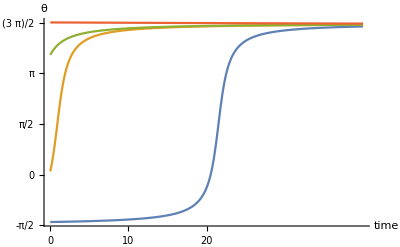

```mathematica
Plot[{θ[-Pi/2+0.1][t]/.soln,θ[0.1][t]/.soln,θ[3Pi/2-1][t]/.soln,θ[3Pi/2+0.01][t]/.soln},{t,0,40},PlotRange->All,AxesLabel->{time,θ},Ticks->{{0,10,20},Table[{Pi/2*val,π/2*val},{val,-1,3}]}]
```

#### Plot cos(θ(t)) vs t.

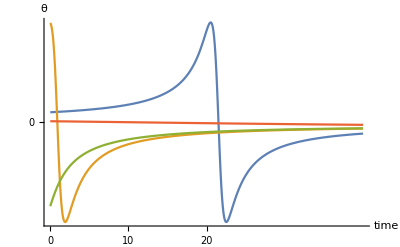

```mathematica
Plot[{Cos[θ[-Pi/2+0.1][t]/.soln],Cos[θ[0.1][t]/.soln],Cos[θ[3Pi/2-1][t]/.soln],Cos[θ[3Pi/2+0.01][t]/.soln]},{t,0,40},PlotRange->All,AxesLabel->{time,θ},Ticks->{{0,10,20},Table[{Pi/2*val,π/2*val},{val,-1,3}]}]
```

Notice that these functions are not monotonic (because cosine is not one-to-one, so various values of θ lead to she same value of cosine(θ)).
There is one V(t) curve that looks “spiky”.  I have isolated it below.
Maybe the shape of the curve makes you think of a heartbeat or the spikes of a neural signal.

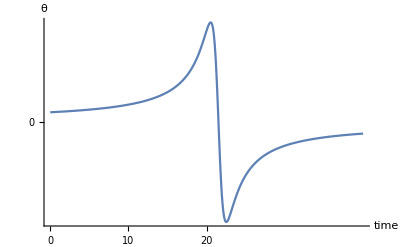

```mathematica
Plot[{Cos[θ[-Pi/2+0.1][t]/.soln]},{t,0,40},PlotRange->All,AxesLabel->{time,θ},Ticks->{{0,10,20},Table[{Pi/2*val,π/2*val},{val,-1,3}]}]
```